```mathematica
<<HypothesisTesting`
```

0.636667

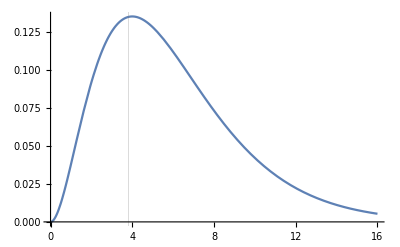

```mathematica
DoF=6;
χ2=3.82;
χ2/DoF
Plot[PDF[ChiSquareDistribution[DoF],x],{x,0,DoF+10},GridLines->{{χ2},{}}]
```

```mathematica
pVal=Integrate[PDF[ChiSquareDistribution[DoF],x],{x,0,χ2}]//N
ChiSquarePValue[χ2,DoF]
```

0.29898

OneSidedPValue→0.29898

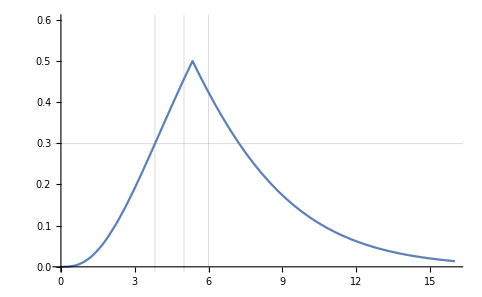

```mathematica
Plot[OneSidedPValue/.ChiSquarePValue[x,DoF],{x,0,DoF+10},PlotRange->{0,0.6},GridLines->{{DoF-1,DoF,χ2},{pVal}}]
```